```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
ClearAll[   eqn,sol,α,kappa,T0,E0,a, b, X0rad, zStart, rEnd, r, θ, Lx, Ly, Lz, x0,y0,z0,sx, sy,x,y,z, tungstenRectangularRegion,tunsgstenSideShell, tungstenMeshRegion,powerDensity3D,powerDensityFun3D, cpsInterFunc]
```

```mathematica
$Assumptions=Lx∈Reals&&Lx>0&&Ly∈Reals&&Ly>0&&Lz∈Reals&&Lz>0 &&x0∈Reals&&y0∈Reals&& z0∈Reals&&sx∈Reals&&sx>0 &&sy∈Reals&&sy>0 &&E0∈Reals&&E0>0&&a∈Reals&&a>0&&b∈Reals&&b>0&&X0rad∈Reals&&X0rad>0;
```

```mathematica
cpsInterFunc=Import["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/kptPower.m"];
```

```mathematica
(*powerDensity3DFunc[x_,y_,z_]:= E0*Exp[- ((x-x0)^2/(2*sx^2)+(y-y0)^2/(2*sy^2))]*b*((b*z/X0rad)^(a-1)*Exp[-b* z/X0rad])/Gamma[a] ;*)
```

```mathematica
(*powerDensity3DFunc[x_,y_,z_]:= Piecewise[{{E0*Exp[- ((x-x0)^2/(2*sx^2)+(y-y0)^2/(2*sy^2))]*b*((b*z)^(a-1)*Exp[-b*z])/Gamma[a],x0-Lx/2≤x≤x0+Lx/2&&y0-Ly/2≤y≤y0+Ly/2&&z0-Lz/2≤z≤z0+Lz/2}},0];*)
```

```mathematica
(*NormIntegral=Integrate[powerDensity3DFunc[x,y,z],{x,x0-Lx/2,x0+Lx/2},{y,y0-Ly/2,y0+Ly/2},{z,z0-Lz/2,z0+Lz/2}]*)
```

```mathematica
(*The water temperature Tim is using in ANSYS is at 35 degrees. With 0.5 W/cm2/K conductivity between water and copper and using the surface area of the sides of the tungsten block ,we get 16 degrees drop between water and copper assuming the water contacts through the full surface of copper plate. If we get another 9 degrees temperature drop in the copper layer plus the the copper-tungsten interface, we would have 25 degree temperature difference between water and tungsten outer layer. That is, the tungsten boundary will be at 60 degrees if the water is at 35 degrees. It is not clear what surface area is given to the copper-to-water contact, so I may use a random coefficient to reduce α.*)
```

```mathematica
α=0.0005/4;(*α=0.0005/1;*)kappa=0.00146;T0=35;Ptot=6.0; minPower=0.00001;
E0=1;a=5.0;b=0.5; X0rad=0.35;
Lx=15.25;Ly=15.25;Lz=10;
x0=0;y0=0;z0=Lz/2;sx=1.5;sy=1.5;
zStart=61.5;rEnd=10;
```

```mathematica
(*powerDensity3D[x_,y_,z_]:= Ptot/NormIntegral*powerDensity3DFunc[x,y,z];*)
```

```mathematica
powerDensity3D[r_,θ_,z_]:=Piecewise[{{Max[cpsInterFunc[z+zStart,r]/1000.,0.0], r≤rEnd}}, 0];
```

```mathematica
(*powerDensity3D[x_,y_,z_]:= Piecewise[{{Ptot/NormIntegral*powerDensity3DFunc[x,y,z], powerDensity3DFunc[x,y,z]>minPower}}, 0];*)
Ptot
```

6.

```mathematica
(*NIntegrate[powerDensity3D[x,y,z],{x,x0-Lx/2,x0+Lx/2},{y,y0-Ly/2,y0+Ly/2},{z,z0-Lz/2,z0+Lz/2}]*)
```

InterpolatingFunction::dmval: Input value {61.5007,0.000714286} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {62.215,0.000714286} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {61.6339,0.133929} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

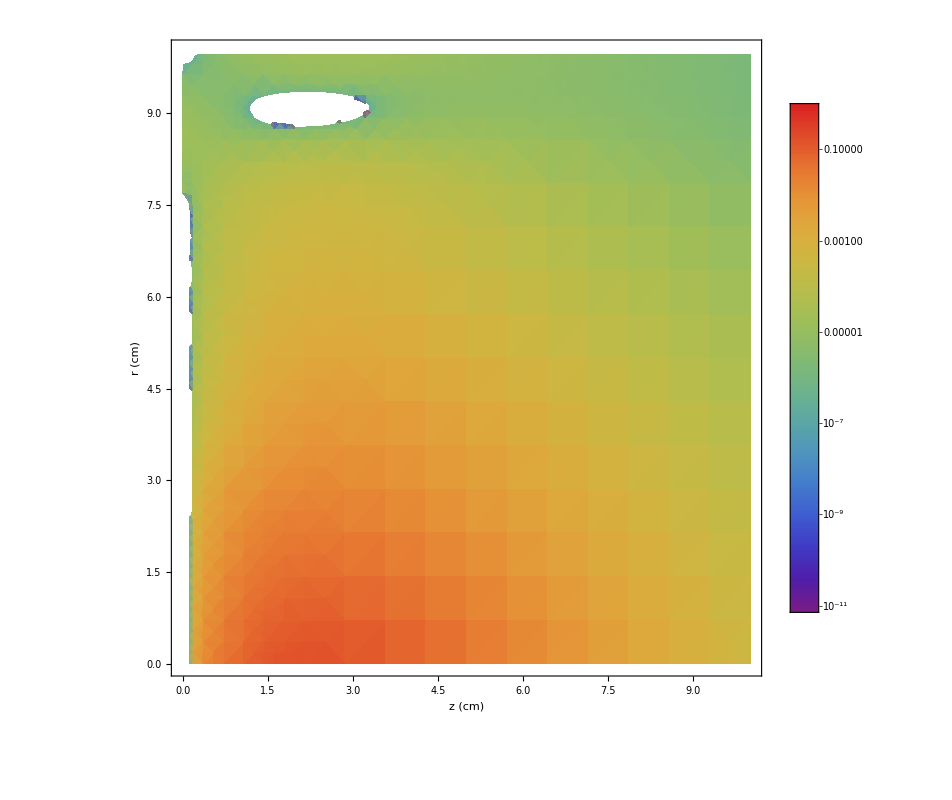

```mathematica
DensityPlot[powerDensity3D[r,0,z],{z,0, Lz},{r,0,rEnd},ColorFunction->{"Rainbow"},PlotRange->Full,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"z (cm)", "r (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->1]
```

InterpolatingFunction::dmval: Input value {64.,0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

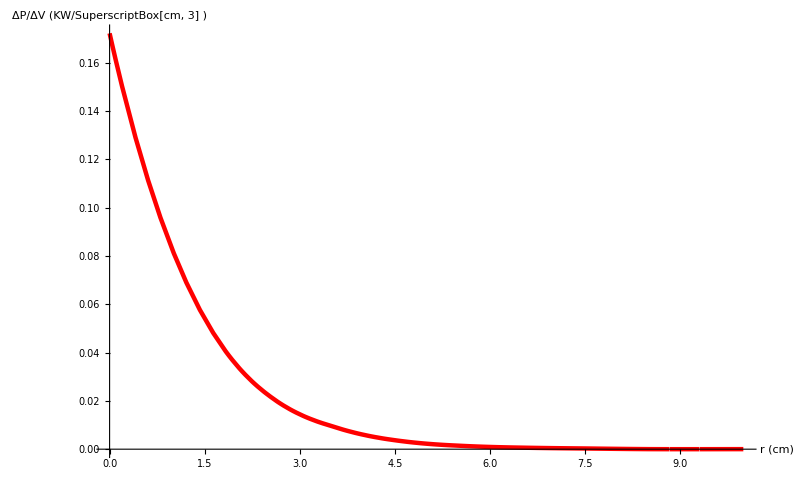

```mathematica
Plot[powerDensity3D[r,0,2.5],{r,0,rEnd},AxesLabel->{"r (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.004]}]
```

InterpolatingFunction::dmval: Input value {61.5002,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

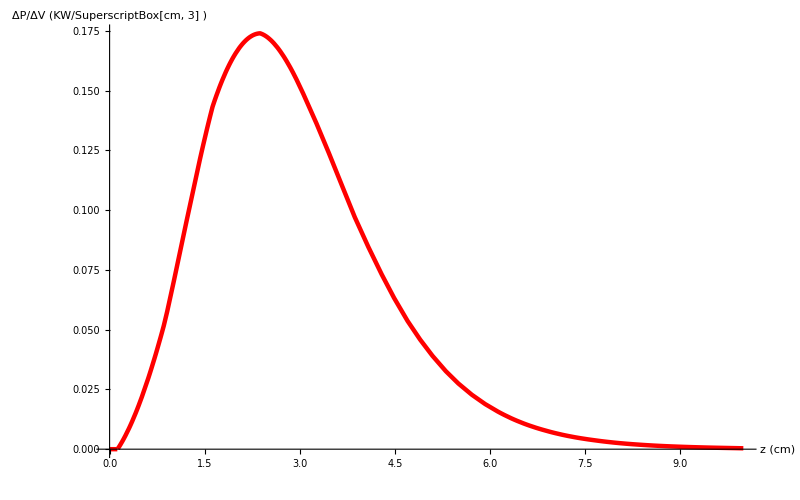

```mathematica
Plot[powerDensity3D[0,0,z],{z,0,Lz}, AxesLabel->{"z (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.004]}]
```

```mathematica
(*tungstenRectangularRegion=Cuboid[{x0-Lx/2,y0-Ly/2,z0-Lz/2},{x0+Lx/2,y0+Ly/2,z0+Lz/2}];*)
(*RegionPlot3D[tungstenRectangularRegion,AxesLabel->Automatic,PerformanceGoal->"Speed",Mesh->None]*)
```

```mathematica
tungstenRectangularRegion=ImplicitRegion[(Abs[r*Cos[θ]]≤Lx/2)&&(Abs[r*Sin[θ]]≤Ly/2),{{r,0,((Lx/2)^2+(Ly/2)^2)^(1/2)},{θ,-π,+π},{z,0,Lz}}];
```

```mathematica
(*tunsgstenSideShell=ImplicitRegion[(Abs[r*Cos[θ]]==Lx/2)||(Abs[r*Sin[θ]]==Ly/2),{{r,0,((Lx/2)^2+(Ly/2)^2)^(1/2)},{θ,0,2*π},{z,0,Lz}}]*)
```

```mathematica
tungstenMeshRegion = ToElementMesh[tungstenRectangularRegion,MeshQualityGoal->"Maximal",MaxBoundaryCellMeasure->{"Length"->0.1},MaxCellMeasure->{"Length"->0.3}];
```

```mathematica
(*eqn=-Laplacian[u[x,y,z],{y,x,z}]==1/kappa*powerDensity3D[x,y,z]+NeumannValue[0.0,{x,y,z}∈RegionBoundary@ tungstenRectangularRegion] ;*)
```

```mathematica
(*sol=NDSolveValue[{eqn,DirichletCondition[ u[x,y,z]==T0, {x==x0-Lx/2||x==x0+Lx/2||y==y0-Ly/2||y==y0+Ly/2}] }, u,{x, y,z} ∈ tungstenRectangularRegion]*)
```

```mathematica
(*eqn=-Laplacian[u[x,y,z],{y,x,z}]==1/kappa*powerDensity3D[x,y,z]+NeumannValue[0.0,{x==x0-Lx/2||x==x0+Lx/2||y==y0-Ly/2||y==y0+Ly/2||z==z0-Lz/2||z==z0+Lz/2}] ;*)
```

```mathematica
(*sol=NDSolveValue[{eqn,u[x0-Lx/2,y,z]==T0, u[x0+Lx/2,y,z]==T0,u[x,y0-Ly/2,z]==T0,u[x,y0+Ly/2,z]==T0  }, u,{x,x0-Lx/2,x0+Lx/2},{y,y0-Ly/2,y0+Ly/2},{z,z0-Lz/2,z0+Lz/2}]*)
```

```mathematica
eqn=-Laplacian[u[r,θ,z],{r,θ,z}, "Cylindrical"]==1/kappa*powerDensity3D[r,θ,z]+NeumannValue[0.0,{z==0||z==Lz}] + NeumannValue[-α/kappa*(u[r,θ,z]-T0),(Abs[r*Cos[θ]]==Lx/2)||(Abs[r*Sin[θ]]==Ly/2)];
```

```mathematica
(*sol=NDSolveValue[eqn  , u,{r, θ, z}∈ tungstenMeshRegion];*)
```

InterpolatingFunction::dmval: Input value {67.4868,0.486705} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {64.8777,0.0882828} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {64.8945,0.0324779} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*sol=NDSolveValue[eqn  , u,{r, 0, rEnd},{θ, 0, 2*π},{z, 0,Lz}]*)
```

```mathematica
(*solAn = DSolve[{eqn,u[x0-Lx/2,y,z]==T0, u[x0+Lx/2,y,z]==T0,u[x,y0-Ly/2,z]==T0,u[x,y0+Ly/2,z]==T0  }, u,{x,x0-Lx/2,x0+Lx/2},{y,y0-Ly/2,y0+Ly/2},{z,z0-Lz/2,z0+Lz/2}];*)
```

```mathematica
sol=Import["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/ResultsForAbsorber/t_distribution_3D_absorber_goodResults.m"]
```

InterpolatingFunction[{{0., 10.0893}, {0., 6.28319}, {0., 10.}}, <>]

```mathematica
(*Export["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/ResultsForAbsorber/t_distribution_3D_absorber_goodResults.m", sol]*)
```

```mathematica
(*With[{r=Sqrt[x^2+y^2],θ=  If[x==0&&y<0, -π,ArcTan[x, y]]}, DensityPlot[sol[r,θ, 0.25], {x, -Lx/2, Lx/2}, {y, -Ly/2, Ly/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0-5,250},ImageSize->{800,800},FrameLabel->{"x (cm)", "y (cm)"(*, "T (^oC)"*)} , LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->1, PlotPoints->200]]*)
```

```mathematica
ParametricPlot3D[{r*Cos[θ], r*Sin[θ],sol[r,θ,2.5]}, {r,0, rEnd},{θ, -π, π},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{{-Lx/2,(+Lx)/2}, { -Ly/2,(+Ly)/2}},ImageSize->{800,800},AxesLabel->{"x (cm)", "y (cm)"(*, "T (^oC)"*)} , LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->1, ViewPoint->{0,0,Infinity}, PlotPoints->200, Axes->{True,True,False}, Mesh->None, Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
(*DensityPlot[sol[(x^2+y^2)^(1/2),ArcTan[x,y],3.5], {x, -Lx/2, Lx/2}, {y, -Ly/2, Ly/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0-5,250},ImageSize->{800,800},AxesLabel->{"x (cm)", "y (cm)"(*, "T (^oC)"*)} , LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->1, PlotPoints->200]*)
```

```mathematica
DensityPlot[sol[r,45*ArcCos[0]/90,z], {z, 0, Lz}, {r,0,((Lx/2)^2+(Ly/2)^2)^(1/2)},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0,250},ImageSize->{800,800},FrameLabel->{"z (cm)", "r (cm)"(*, "T (^oC)"*)} , LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->1, PlotPoints->200]
```

-Graphics-

```mathematica
DensityPlot[sol[r,θ,2.5], {θ, -π, π}, {r,0,((Lx/2)^2+(Ly/2)^2)^(1/2)},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0-5,250},ImageSize->{800,800},FrameLabel->{"θ (rad)", "r (cm)"(*, "T (^oC)"*)} , LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->1, PlotPoints->200]
```

-Graphics-

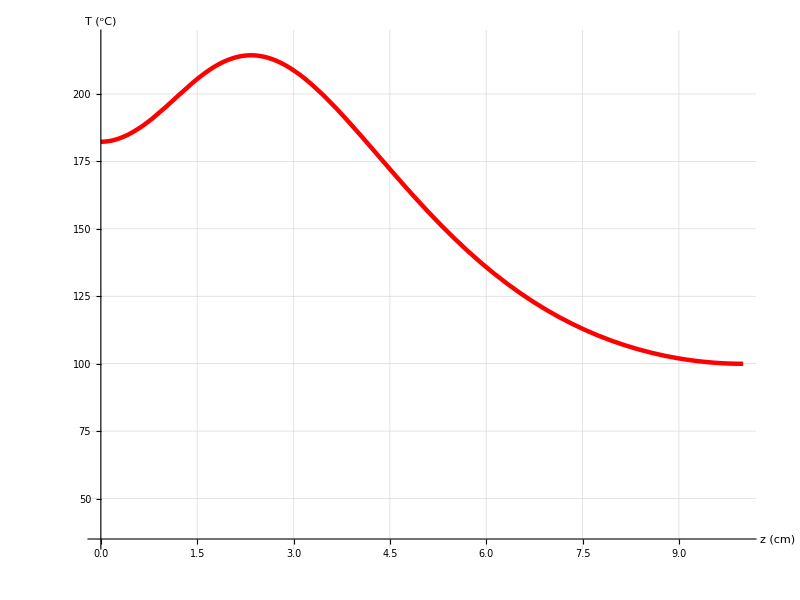

```mathematica
Plot[sol[0,45*ArcCos[0]/90,z], {z,0,Lz},GridLines->Automatic,PlotRange->{T0,220},AxesLabel->{"z (cm)", "T (^oC)"} ,LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,600}, PlotStyle->{Red,Thickness[0.004]}]
```

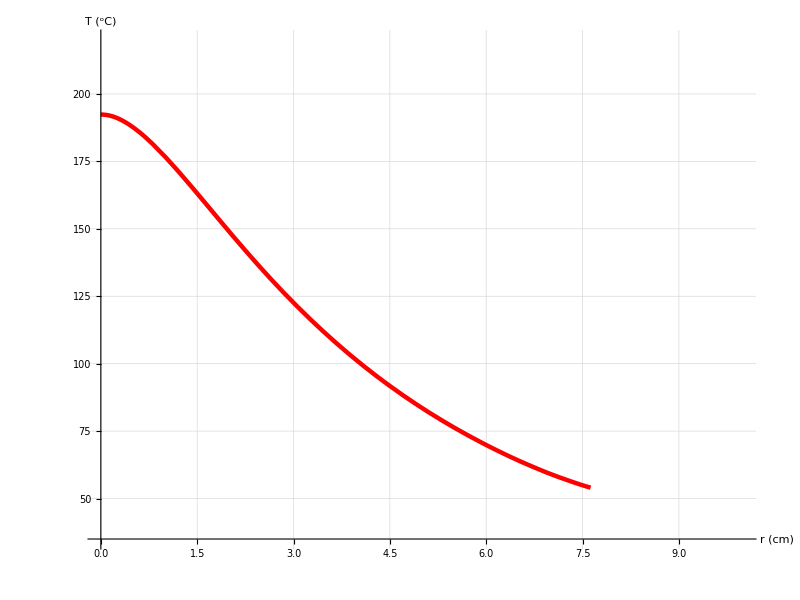

```mathematica
Plot[sol[r,90*ArcCos[0]/90,2.5], {r, 0,rEnd},GridLines->Automatic,PlotRange->{{0,10},{T0,220}},AxesLabel->{"r (cm)", "T (^oC)"} ,LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,600}, PlotStyle->{Red,Thickness[0.004]}]
```

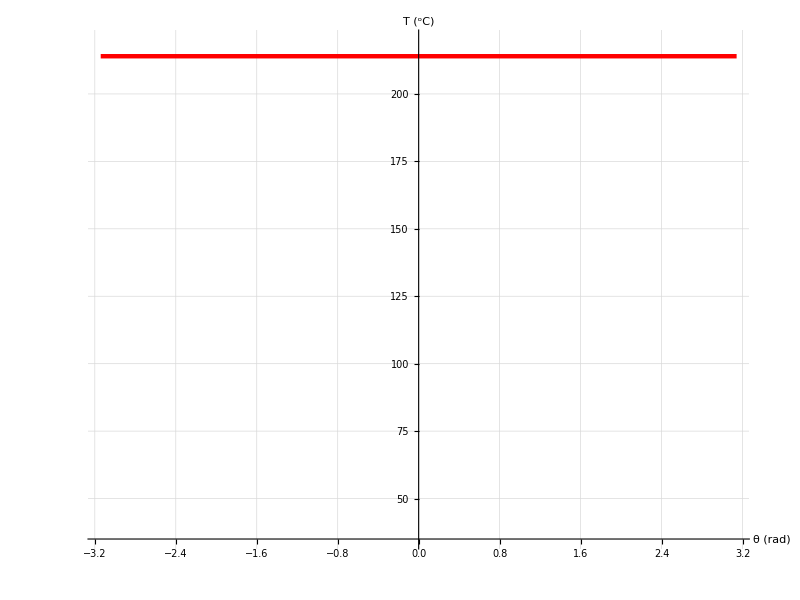

```mathematica
Plot[sol[0,θ,2.5], {θ, -π,+π},GridLines->Automatic,PlotRange->{T0,220},AxesLabel->{"θ (rad)", "T (^oC)"} ,LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,600}, PlotStyle->{Red,Thickness[0.004]}]
```